```mathematica
sol = DSolve[y''[x]+x*y'[x]==0,y[x],x]
```

{{y[x]→C[2]+√(π/2) C[1] Erf[x/(√2)]}}

```mathematica
ode = y''[x]+x*y'[x]==0
```

x y'[x]+y''[x]==0

```mathematica
ode/.sol
```

{x y'[x]+y''[x]==0}

```mathematica
ode/.D[sol, x, x] /.D[sol,x]
```

{{True}}

```mathematica
DSolve[{y''[x]-x y'[x]==0,y[0]==0,y'[0]==1},y[x],x]
```

{{y[x]→√(π/2) Erfi[x/(√2)]}}

```mathematica
DSolve[{x'[t]==y[t],y'[t]==-a^2 x[t],x[0]==1,y[0]==0},{x[t],y[t]},t]
```

{{x[t]→Cos[a t],y[t]→-a Sin[a t]}}

```mathematica
solNew=DSolve[{x'[t]==y[t],y'[t]==-a^2 x[t],x[0]==1,y[0]==0},{x,y},{t}]
```

{{x→Function[{t},Cos[a t]],y→Function[{t},-a Sin[a t]]}}

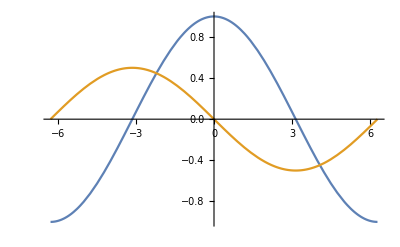

```mathematica
Plot[Evaluate[{x[t],y[t]}/.solNew/.a->1/2],{t,-2 Pi,2 Pi}]
```

```mathematica
nlocs=DSolve[{x'[t]==y[t],y'[t]==-x[t]-0.7 Cos[0.3 t] Sin[x[t]],x[0]==1,y[0]==0},{x,y},{t}]
```

DSolve[{x'[t]==y[t],y'[t]==-0.7 Cos[0.3 t] Sin[x[t]]-x[t],x[0]==1,y[0]==0},{x,y},{t}]

```mathematica
nlocs=NDSolve[{x'[t]==y[t],y'[t]==-x[t]-0.7 Cos[0.3 t] Sin[x[t]],x[0]==1,y[0]==0},{x,y},{t,0,13 Pi}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

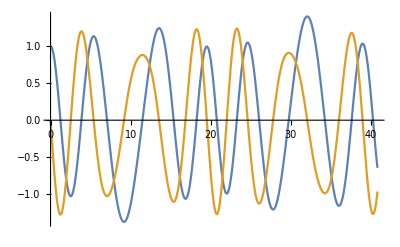

```mathematica
Plot[Evaluate[{x[t], y[t]}/.nlocs],{t, 0, 13Pi}]
```

```mathematica
{x[1], y[1]}/.nlocs
```

{{0.299017,-1.21722}}

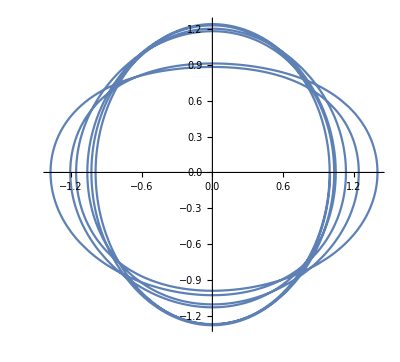

```mathematica
ParametricPlot[Evaluate[{x[t], y[t]}/.nlocs],{t, 0, 13Pi}]
```

```mathematica
Parameters[a_, b_, c_, d_, x0_,y0_ ]:=Module[{solve},
solve = NDSolve[{y'[t]==(c*x[t]-d)*y[t],x'[t]==(a-b*y[t])*x[t], x[0]==x0, y[0]==y0},{y, x},{ t, 0, 15}];
Return[solve]]
```

```mathematica
(*Модель Лотки-Вольтерры*)
```

```mathematica
(*Задача 1*)
```

```mathematica
sol1 = Parameters[1,2, 1.5, 1.5, 1, 1]
```

{{y→InterpolatingFunction[…],x→InterpolatingFunction[…]}}

```mathematica
(*Задача 2*)
```

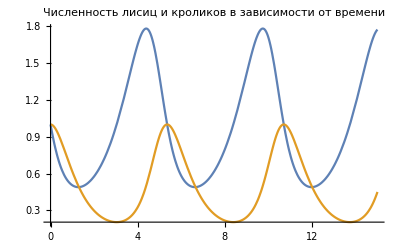

```mathematica
Plot[Evaluate[{x[t], y[t]}/.sol1],{t, 0, 15}, PlotLabel->"Численность лисиц и кроликов в зависимости от времени"]
```

```mathematica
(*по оси х - время, по оси у - численность, синим - кролики, оранжевым - лисы*)
```

```mathematica
pltX1 = ParametricPlot[Evaluate[{x[t],x'[t]}/.sol1], {t, 0, 15}, PlotStyle->Gray];
```

```mathematica
pltY1 = ParametricPlot[Evaluate[{y[t], y'[t]}/.sol1],{t,0,15}, PlotStyle->Orange];
```

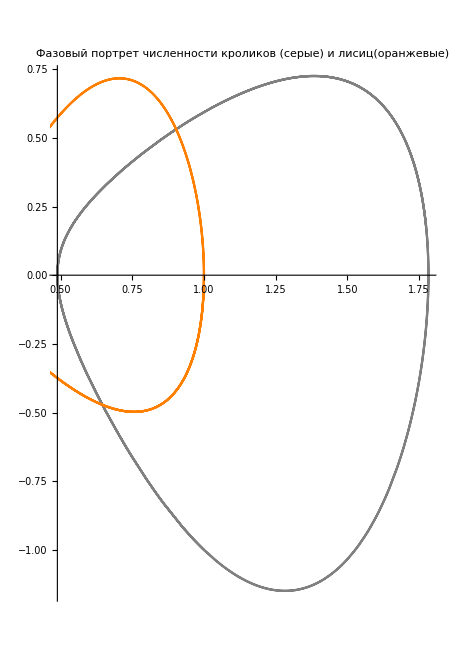

```mathematica
Show[pltX1, pltY1, PlotLabel->"Фазовый портрет численности кроликов (серые) и лисиц(оранжевые)"]
```

```mathematica
(*фазовый портрет, по оси у -скорость, по оси х - численность*)
```

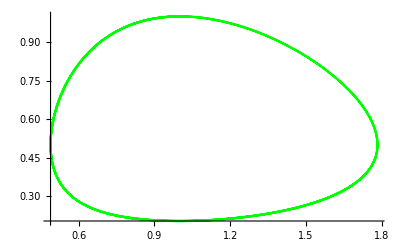

```mathematica
ParametricPlot[Evaluate[{x[t], y[t]}/.sol1], {t, 0, 15}, PlotStyle->Green]
```

```mathematica
(*фазовый портрет: по оси х кролики, по оси у - лисы*)
```

```mathematica
(*Задача 3*)
```

```mathematica
sol31 = Parameters[1,2, 1.5, 1.5, 0.5, 0.5];
```

```mathematica
plt31 = ParametricPlot[Evaluate[{x[t], y[t]}/.sol31], {t, 0, 15}, PlotStyle->Red];
```

```mathematica
sol32 = Parameters[1,2, 1.5, 1.5, 1, 1.5];
```

```mathematica
plt32 = ParametricPlot[Evaluate[{x[t], y[t]}/.sol32], {t, 0, 15}, PlotStyle->Orange];
```

```mathematica
sol33 = Parameters[1,2, 1.5, 1.5, 2,2];
```

```mathematica
plt33 = ParametricPlot[Evaluate[{x[t], y[t]}/.sol33], {t, 0, 15}, PlotStyle->Yellow];
```

```mathematica
sol34 = Parameters[1,2, 1.5, 1.5, 2.5, 2];
```

```mathematica
plt34 = ParametricPlot[Evaluate[{x[t], y[t]}/.sol34], {t, 0, 15}, PlotStyle->Green];
```

```mathematica
sol35 = Parameters[1,2, 1.5, 1.5, 3, 2];
```

```mathematica
plt35 = ParametricPlot[Evaluate[{x[t], y[t]}/.sol35], {t, 0, 15}, PlotStyle->Blue];
```

```mathematica
sol36 = Parameters[1,2, 1.5, 1.5, 4, 4];
```

```mathematica
plt36 = ParametricPlot[Evaluate[{x[t], y[t]}/.sol36], {t, 0, 15}, PlotStyle->Purple];
```

```mathematica
special = NSolve[{(1-2*y)*x == 0, (1.5*x-1.5)*y == 0}]
```

{{x→1.,y→0.5},{x→0.,y→0.}}

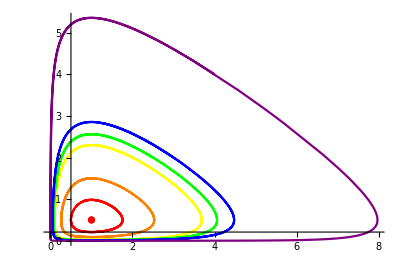

```mathematica
Show[plt31, plt32, plt33, plt34, plt35,plt36,ListPlot[{{1,0.5}}, PlotStyle->Red], PlotRange->All]
```

```mathematica
(*В зависимости от х0 и у0 фазовые портреты выглядят не так плавно, особая точка, вокруг которой кривые располагаются - 1,0.5*)
```

```mathematica
(*Задача 4*)
```

```mathematica
sol41 = Parameters[1,2, 1.5, 1.5, 2, 2];
```

```mathematica
plt41 = ParametricPlot[Evaluate[{x[t], y[t]}/.sol41], {t, 0, 15}, PlotStyle->Red];
```

```mathematica
sol42 = Parameters[2,2, 1.5, 1.5, 2, 2];
```

```mathematica
plt42 = ParametricPlot[Evaluate[{x[t], y[t]}/.sol42], {t, 0, 15}, PlotStyle->Orange];
```

```mathematica
sol43 = Parameters[1,3, 1.5, 1.5, 2, 2];
```

```mathematica
plt43 = ParametricPlot[Evaluate[{x[t], y[t]}/.sol43], {t, 0, 15}, PlotStyle->Yellow];
```

```mathematica
sol44 = Parameters[2,3, 1.5, 1.5, 2, 2];
```

```mathematica
plt44 = ParametricPlot[Evaluate[{x[t], y[t]}/.sol44], {t, 0, 15}, PlotStyle->Green];
```

```mathematica
sol45 = Parameters[3,4, 1.5, 1.5, 2, 2];
```

```mathematica
plt45 = ParametricPlot[Evaluate[{x[t], y[t]}/.sol45], {t, 0, 15}, PlotStyle->Blue];
```

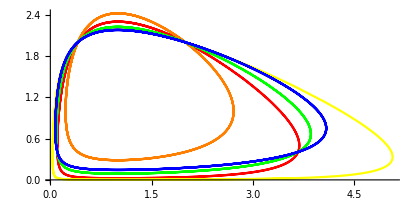

```mathematica
Show[plt41, plt42, plt43, plt44, plt45, PlotRange->All]
```

```mathematica
Manipulate[ParametricPlot[Evaluate[{x[t], y[t]}/.Parameters[a,b, 1.5, 1.5, 2, 2]], {t, 0, 15}, PlotStyle->Blue], {a, 0, 5, 0.5}, {b, 0, 5,0.5}]
```

```mathematica
(*а влияет на скорость роста популяции кроликов, b - на скорость ее вымирания*)
```

```mathematica
Manipulate[ParametricPlot[Evaluate[{x[t], y[t]}/.Parameters[1,1,c, d, 2, 2]], {t, 0, 15}, PlotStyle->Blue], {c, 0, 5, 0.5}, {d, 0, 5,0.5}]
```

```mathematica
(*c влияет на скорость роста популяции и d - на скорость вымирания лис*)
```

```mathematica
(*Модель Лотки-Вольтерры и внутривидовая
конкуренция*)
```

```mathematica
ParametersNew[a1_,a2_, b12_,b21_, c1_,c2_, x0_,y0_ ]:=Module[{solve},
solve = NDSolve[{x'[t]==(a1 +b12*y[t] - c1*x[t])*x[t],y'[t]==(a2+b21*x[t]-c2*y[t])*y[t], x[0]==x0, y[0]==y0},{y, x},{ t, 0, 660}];
Return[solve]]
```

```mathematica
(*Задача 5*)
```

```mathematica
sol51 = ParametersNew[1.5, -1.5, -2, 1.5, 0.01, 0.01, 1, 1]
```

{{y→InterpolatingFunction[…],x→InterpolatingFunction[…]}}

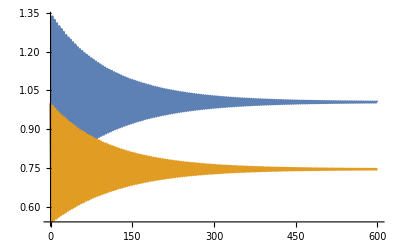

```mathematica
Plot[Evaluate[{x[t], y[t]}/.sol51],{t, 0, 600}]
```

```mathematica
(*Колебания затухают и стабилизируются, потому что популяция с конкуренцией стремится к устойчивому значению*)
```

```mathematica
(*Задача 6*)
```

```mathematica
pltX5 = ParametricPlot[Evaluate[{x[t],x'[t]}/.sol51], {t, 0, 660}, PlotStyle->Gray];
```

```mathematica
pltY5= ParametricPlot[Evaluate[{y[t],y'[t]}/.sol51], {t, 0, 660}, PlotStyle->Orange];
```

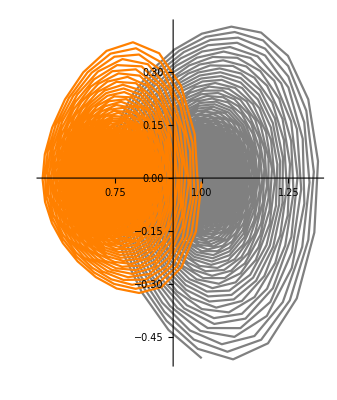

```mathematica
Show[pltX5, pltY5, PlotRange->All]
```

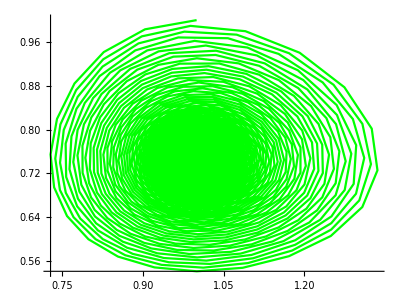

```mathematica
ParametricPlot[Evaluate[{x[t], y[t]}/.sol51], {t, 0, 660}, PlotStyle->Green, PlotRange->All]
```

```mathematica
(*в данной модели графики незамкнуты, так как популяция зависит сама от себя и постоянно меняется: чем меньше кроликов - тем больше кроликов*)
```